```mathematica
<<PCA.m

faces = LoadFaces[100];
flatFaces = FlattenImage /@ faces;
```

```mathematica
eigenfaces = EigenFaces[faces, 100]
```

{1}
 |  |  |  |

```mathematica
FormatFace /@ eigenfaces;
```

```mathematica
avg = N[Total[flatFaces]]/Length[flatFaces];
```

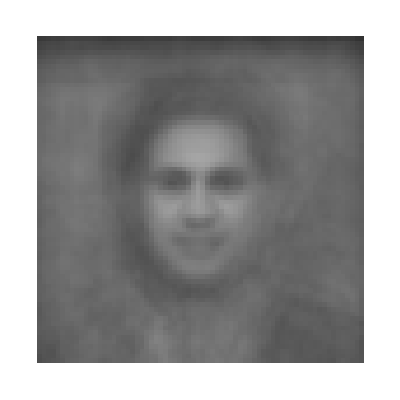

```mathematica
(FormatFace /@ (Function[x,avg ] /@ eigenfaces))[[1]]
```

```mathematica
face = FlattenImage[faces[[1]]];
```

```mathematica
decon = eigenfaces.face;
```

```mathematica
recon = Transpose[eigenfaces].decon;
```

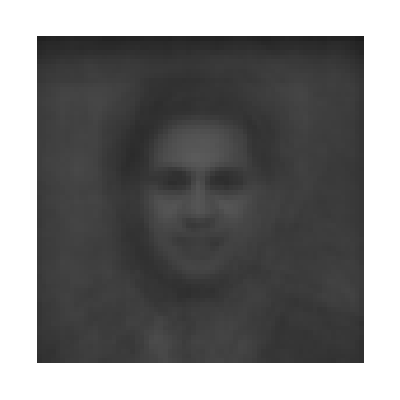

```mathematica
FormatFace[Function[x,  x / 100000] @ recon]
```

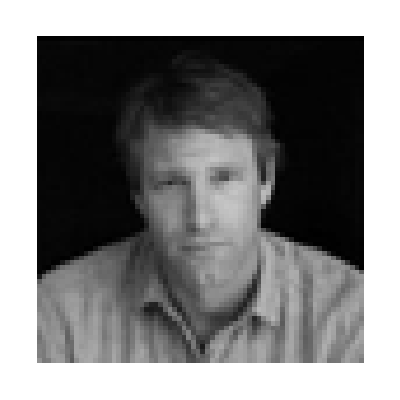

```mathematica
FormatFace[face]
```

```mathematica
(Transpose[eigenfaces].eigenfaces)[[1;;5,1;;5]]
```

{{12.0013,11.9019,11.9303,12.0268,11.9634},{11.9019,12.0551,12.3345,12.4313,12.4099},{11.9303,12.3345,13.2375,13.4978,13.5259},{12.0268,12.4313,13.4978,14.5477,14.7888},{11.9634,12.4099,13.5259,14.7888,15.1926}}

```mathematica
Dot[Transpose[eigenfaces], eigenfaces]
```

{{0.0156418,0.0142925,0.0120667,0.0110211,0.0099197,4890,-0.00230867,-0.00158933,-0.0019367,-0.00138492,-0.000496545},4898,{1}}
 |  |  |  |